### Stochastic Langevin Dynamics

#### Additive noise

See Figure 2 in paper Shaping the Epigenetic Landscape: Complexities and Consequences

2.92484×10^-7

0.0239801

0.240209

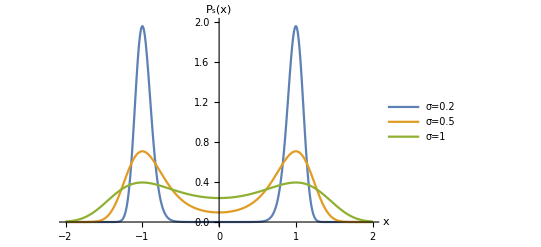

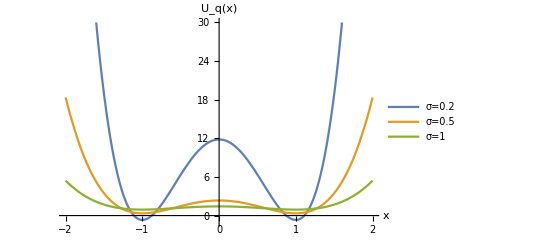

```mathematica
U[x_]:=x^4/4-x^2/2;
f[x_]:=-U'[x];
g[x_,σ_]:=σ;
α=0; (* ito *)
Valuesσ={0.2,0.5,1};
Stepsize=0.00001;
Ps[x_,σ_,N_]:=N/σ^2 Exp[-2/σ^2 U[x]];  (* eq 9 *)
Uq[x_,σ_,N_]:=2U[x]/σ^2+Log[σ^2/N]; (* eq 10 *)
(* Uq2[x_,σ_,N_]:=-Log[N/σ^2Exp[-2/σ^2U[x]]]; *)

σ=σlow=0.2;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nlow=N/.Nvalue[[1]];
Print[Nlow]

σ=σmid=0.5;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area2=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area2==1,N];
Nmid=N/.Nvalue[[1]];
Print[Nmid]

σ=σhigh=1;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area3=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area3==1,N];
Nhigh=N/.Nvalue[[1]];
Print[Nhigh]

Plot[{Evaluate[Ps[x,σlow,Nlow]],Evaluate[Ps[x,σmid,Nmid]],Evaluate[Ps[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{0,2},AxesLabel->{"x","P_s(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
Plot[{Evaluate[Uq[x,σlow,Nlow]],Evaluate[Uq[x,σmid,Nmid]],Evaluate[Uq[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,30},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
(* Plot[{Evaluate[Uq2[x,σlow,Nlow]],Evaluate[Uq2[x,σmid,Nmid]],Evaluate[Uq2[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,30},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}] *)
```

#### Multiplicative noise

Example 1: Shifting the fixed points
See Figure 3 in paper

2.6575×10^-53

-0.439111

1.41427×10^-9

0.00569356

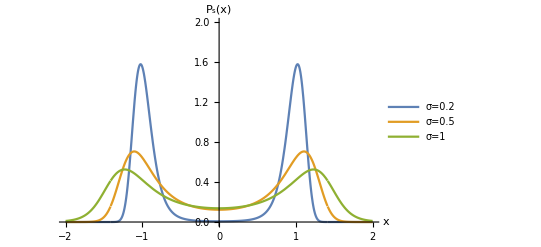

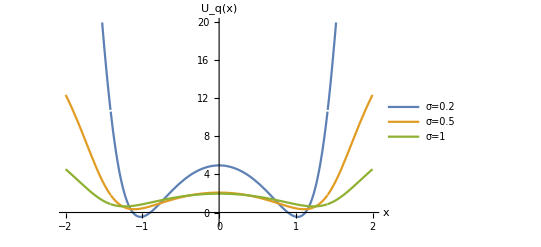

```mathematica
U[x_]:=x^4/4-x^2/2;
f[x_]:=-U'[x];
g[x_,σ_]:=σ/4(x^4-4 x^2+8);
α=0; (* ito *)
Valuesσ={0.2,0.5,1};
Stepsize=0.01;
IntegrationConstant[σ_]=1/σ^2(ArcTan[1]+3/2)+2 α Log[8];
(* IntegrationConstant[σ_]=1; *)
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Ps[x_,σ_,N_]:=16 N/σ^2 Exp[2(α-1)Log[x^4-4 x^2+8]+1/σ^2(ArcTan[1-x^2/2]-2(x^2-6)/(x^4-4 x^2+8)+IntegrationConstant[σ])]; (* eq 11 *)
(* Uq[x_,σ_,N_]:=Log[σ^2/(16 N) (x^4-x^2+8)^(2(1-α))]-1/σ^2(ArcTan[1-x^2/2]-(2 (x^2-6))/(x^4-x^2+8))-IntegrationConstant[σ]; (* eq 12 *) *)
Uq[x_,σ_,N_]:=-Log[16 N/σ^2 Exp[2(α-1)Log[x^4-4 x^2+8]+1/σ^2(ArcTan[1-x^2/2]-2(x^2-6)/(x^4-4 x^2+8)+IntegrationConstant[σ])]]; 

σ=σlow=0.2;
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area1=Sum[TrapezoidalRulePs[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nlow=N/.Nvalue[[1]];
Print[Nlow]
Print[Uq[1,σlow,Nlow]]

σ=σmid=0.5;
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area2=Sum[TrapezoidalRulePs[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area2==1,N];
Nmid=N/.Nvalue[[1]];
Print[Nmid]

σ=σhigh=1;
TrapezoidalRulePs[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area3=Sum[TrapezoidalRulePs[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area3==1,N];
Nhigh=N/.Nvalue[[1]];
Print[Nhigh]

Plot[{Evaluate[Ps[x,σlow,Nlow]],Evaluate[Ps[x,σmid,Nmid]],Evaluate[Ps[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{0,2},AxesLabel->{"x","P_s(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
Plot[{Evaluate[Uq[x,σlow,Nlow]],Evaluate[Uq[x,σmid,Nmid]],Evaluate[Uq[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,20},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
```

Example 2: Creation and destruction of fixed points
See Figure 4 in paper

0.0000691993

0.0864627

0.573664

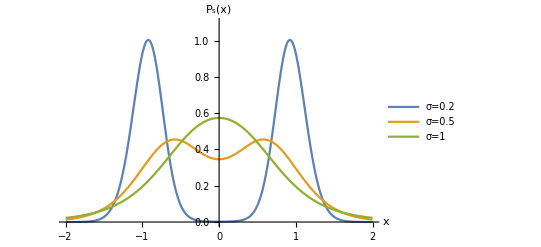

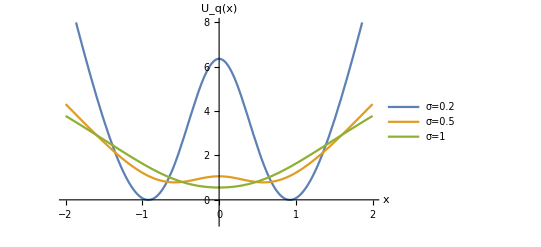

```mathematica
U[x_]:=(x^4/4-x^2/2);
f[x_]:=-U'[x];
g[x_,σ_]:=σ(1+x^2);
α=0; (* ito *)
Valuesσ={0.2,0.5,1};
Stepsize=0.00001;

IntegrationConstant[σ_]:=2;
Ps[x_,σ_,N_]:=N/(σ^2(1+x^2)^2)Exp[1/σ^2((2 α σ^2-1)Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ])]; (* eq 13 *)
Uq[x_,σ_,N_]:=Log[σ^2 (1+x^2)^2/N]-1/σ^2 ((2 α σ^2-1) Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ]); (* eq 14 *)

σ=σlow=0.2;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nlow=N/.Nvalue[[1]];
Print[Nlow]

σ=σmid=0.5;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area2=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area2==1,N];
Nmid=N/.Nvalue[[1]];
Print[Nmid]

σ=σhigh=1;
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,N]+Ps[b,σ,N]);
Area3=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area3==1,N];
Nhigh=N/.Nvalue[[1]];
Print[Nhigh]


Plot[{Evaluate[Ps[x,σlow,Nlow]],Evaluate[Ps[x,σmid,Nmid]],Evaluate[Ps[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{0,1.1},AxesLabel->{"x","P_s(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
Plot[{Evaluate[Uq[x,σlow,Nlow]],Evaluate[Uq[x,σmid,Nmid]],Evaluate[Uq[x,σhigh,Nhigh]]},{x,-2,2},PlotRange->{-1,8},AxesLabel->{"x","U_q(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"}]
```

Figure 5 in paper

0.23862

0.154879

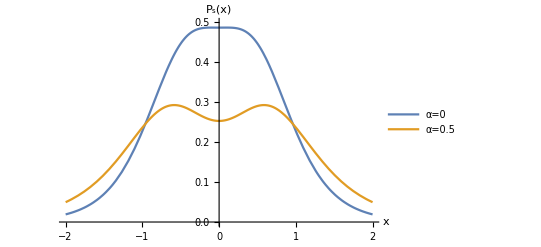

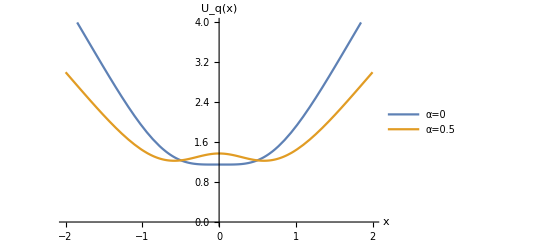

```mathematica
U[x_]:=x^4/4-x^2/2;
f[x_]:=-U'[x];
σ=0.7;
g[x_,σ_]:=σ(1+x^2);
Valuesσ={0.2,0.5,1};
Stepsize=0.00001;
IntegrationConstant[σ_]:=2;
Ps[x_,σ_,α_,N_]:=N/(σ^2(1+x^2)^2)Exp[1/σ^2((2 α σ^2-1)Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ])]; (* eq 13 *)
Uq[x_,σ_,α_,N_]:=Log[σ^2 (1+x^2)^2/N]-1/σ^2 ((2 α σ^2-1) Log[1+x^2]-2/(1+x^2)+IntegrationConstant[σ]); (* eq 14 *)

α=αito=0; (* ito *)
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,αito,N]+Ps[b,σ,αito,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nito=N/.Nvalue[[1]];
Print[Nito]

α=αstra=0.5; 
TrapezoidalRule[a_,b_]=(b-a)*0.5*(Ps[a,σ,αstra,N]+Ps[b,σ,αstra,N]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
Nstra=N/.Nvalue[[1]];
Print[Nstra]

Plot[{Evaluate[Ps[x,σ,αito,Nito]],Evaluate[Ps[x,αstra,Nc]]},{x,-2,2},PlotRange->{0,0.5},AxesLabel->{"x","P_s(x)"},PlotLegends->{"α=0","α=0.5"}]
Plot[{Evaluate[Uq[x,σ,αito,Nstra]],Evaluate[Uq[x,αstra,Nc]]},{x,-2,2},PlotRange->{0,4},AxesLabel->{"x","U_q(x)"},PlotLegends->{"α=0","α=0.5"}]
```

### Adding additive and multiplicative noise to double well potential with perturbation

Potential 1 is the potential function used in the “Shaping the epigenetic landscape” paper with the perturbation
Potential 2 is the potential function used in the “Enhancing transport by shaping barriers” paper with the perturbation
I have commented out  different combinations of potentials and noise functions, and I have added whether they work or not.

2.92442×10^-7

0.0233489

0.237101

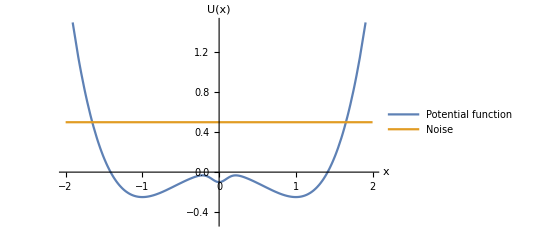

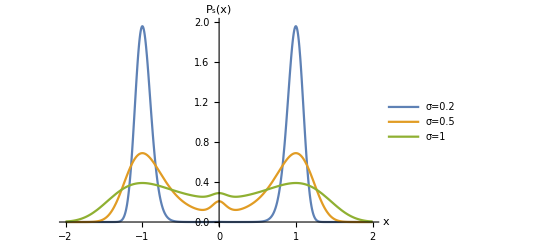

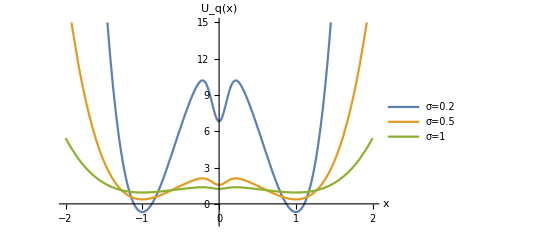

```mathematica
(* Plot potential and noise *)
ClearAll[U,f,g,Ps,Uq]

(* Additive noise added to potential 1 with perturbation: this works *)
U[x_]:=(x^4/4-x^2/2) +(-a Exp[-b (x+d)^2]);
g[x_,σ_]:=σ;
IntegrationConstant[σ_]:=0;
a=0.1;
b=50;
d=0; 


(* Multiplicative noise 1 added to potential 1 with perturbation: does NOT work *)
(* U[x_]:=(x^4/4-x^2/2) +(-a Exp[-b (x+d)^2]);
g[x_,σ_]:=σ/4(x^4-4.0 x^2+8);
IntegrationConstant[σ_]:=1/σ^2(ArcTan[1]+3/2)+2 α Log[8];
a=0.3;
b=50;
d=0; *)


(* Multiplicative noise 1 added to potential 1 wihout perturbation: this works *)
(* U[x_]:=(x^4/4-x^2/2);
g[x_,σ_]:=σ/4(x^4-4.0 x^2+8);
IntegrationConstant[σ_]:=1/σ^2(ArcTan[1]+3/2)+2 α Log[8]; *)


(* Multiplicative noise 2 added to potential 1: this works *)
(* U[x_]:=(x^4/4-x^2/2) +(-a Exp[-b (x+d)^2]);
g[x_,σ_]:=σ(1+x^2);
IntegrationConstant[σ_]:=2;
a=0.1;
b=50;
d=0; *)


(* Additive noise added to potential 2 with perturbation: does NOT work *)
(* U[x_]:=h(1-(2 x/s[x])^2)^2 (1-a Exp[-b (x+d)^2]);
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];
g[x_,σ_]:=σ;
IntegrationConstant[σ_]:=0;
a=0.3;
b=200;
d=0.2; *)


(* Additive noise added to potential 2 without perturbation: does NOT work *)
(* U[x_]:=h(1-(2 x/s[x])^2)^2;
s[x_]:=c HeavisideTheta[-x]+(2-c) HeavisideTheta[x];
g[x_,σ_]:=σ;
IntegrationConstant[σ_]:=0;
 *)


(* Additive noise added to simplified version of potential 2 without perturbation: this works *)
(* U[x_]:=h(1-(2 x)^2)^2;
g[x_,σ_]:=σ;
IntegrationConstant[σ_]:=0; *)
 


Ps[x_,N_,σ_]:=N/g[x,σ]^2 Exp[2 Int[x,σ]];
Uq[x_,N_,σ_]:=Log[g[x,σ]^2/N]-2Int[x,σ];

Int[x_,σ_]:=Integrate[(f[x]+α g[x,σ] g'[x,σ])/(g[x,σ]^2),x]+IntegrationConstant[σ];

f[x_]:=-U'[x];

h=0.5;
c=1;
α=0; (* ito *)

Stepsize=0.01;

(* Probability distribution and probabilistic landscape for σ=0.2 *)
σ=0.2;
TrapezoidalRule[u_,v_]=(v-u)*0.5*(Ps[u,N,σ]+Ps[v,N,σ]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
(* Print[Nvalue] *)
Nstraσ02=N/.Nvalue[[1]];
Print[Nstraσ02]

(* Probability distribution and probabilistic landscape for σ=0.5 *)
σ=0.5;
TrapezoidalRule[u_,v_]=(v-u)*0.5*(Ps[u,N,σ]+Ps[v,N,σ]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
(* Print[Nvalue] *)
Nstraσ05=N/.Nvalue[[1]];
Print[Nstraσ05]

(* Probability distribution and probabilistic landscape for σ=0.5 *)
σ=1;
TrapezoidalRule[u_,v_]=(v-u)*0.5*(Ps[u,N,σ]+Ps[v,N,σ]);
Area1=Sum[TrapezoidalRule[i,i+Stepsize],{i,-2,2,Stepsize}];
Nvalue=NSolve[Area1==1,N];
(* Print[Nvalue] *)
Nstraσ1=N/.Nvalue[[1]];
Print[Nstraσ1]

Plot[{U[x],g[x,0.5]},{x,-2,2},AxesLabel->{"x","U(x)"},PlotRange->{-0.5,1.5},PlotLegends->{"Potential function", "Noise"}]
Plot[{Evaluate[Ps[x,Nstraσ02,0.2]],Evaluate[Ps[x,Nstraσ05,0.5]],Evaluate[Ps[x,Nstraσ1,1]]},{x,-2,2},AxesLabel->{"x","P_s(x)"},PlotLegends->{"σ=0.2","σ=0.5","σ=1"},PlotRange->{0,2}]
Plot[{Evaluate[Uq[x, Nstraσ02,0.2]],Evaluate[Uq[x, Nstraσ05,0.5]],Evaluate[Uq[x, Nstraσ1,1]]},{x,-2,2},PlotLegends->{"σ=0.2","σ=0.5","σ=1"},AxesLabel->{"x","U_q(x)"},PlotRange->{-1.5,15}]
```